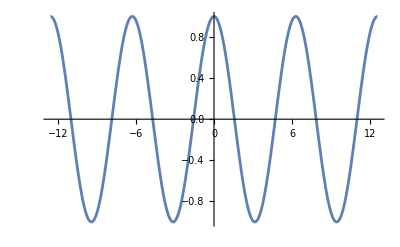

```mathematica
f[x_]:= Cos[x];
originalRange={-4*Pi,4*Pi,0.1};
range=originalRange;

pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]];
Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Join[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]

LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]

approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
error[af_]:=Quiet[Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}],General::munfl]
errorFunc[xii_, w_]:=error[approxFunc[xii,w]]
```

```mathematica
xiiRange=range;wRange=range; (*Tweak these for faster initial evaluation times *)

search[anything___]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progressMap[search,Range[20]]
```

$Aborted

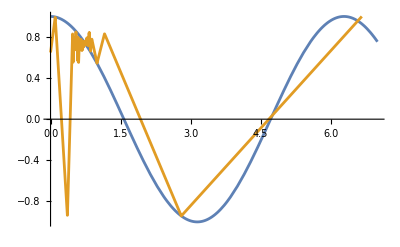

```mathematica
aFunc= approxFunc@@minP;
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

```mathematica
minP
minV
```

{2.8,0.1}

8.70434

## Numerical minimization

```mathematica
range[[3]]=originalRange[[3]]/5;

aFunc= approxFunc@@minP;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

plots={};
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

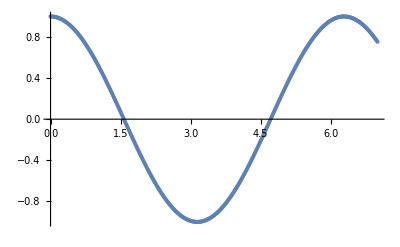

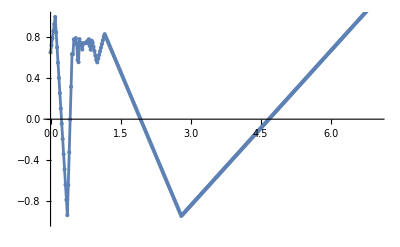

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

```mathematica
aValsHist={aVals};
progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[15] , "Optimized"];
bestVals=aValsHist[[First[PositionSmallest[ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]];
aFunc=funcFromVals[bestVals];
```

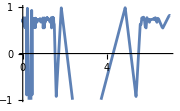
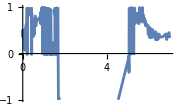
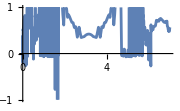
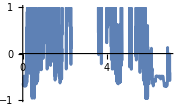
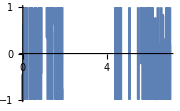

```mathematica
ParallelMap[With[{aFunc=funcFromVals[aValsHist[[#]]]},Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]]&, Round/@Subdivide[1, Length[aValsHist], 4]]
```

-Graphics-

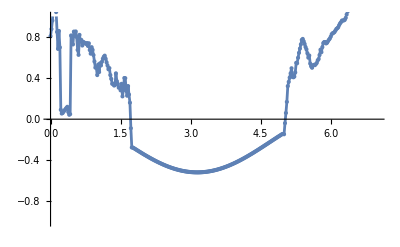

```mathematica
PlotVals[fVals]
PlotVals[bestVals]
```

```mathematica
"Original Error:"
e1=error[approxFunc@@minP]
"Optimized Error:"
e2=error[aFunc]
approximation=If[e1<e2,approxFunc@@minP, aFunc];
```

Original Error:

44.2167

Optimized Error:

15.3998

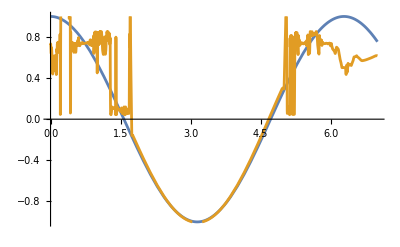

```mathematica
Plot[{f[x], approximation[approximation[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```